```mathematica
(* Граници на числови редици *)
Limit[(-3 n+7)/(2 n-5),n->Infinity]
```

-3/2

```mathematica
Limit[(2 n^3-3 n+7)/(5 n^3+n^2-1),n->∞]
```

2/5

```mathematica
Limit[(1+a/n)^n,n->∞]
```

ⅇ^a

```mathematica
Limit[(1+3/(2 n-1))^3,n->∞]
```

1

```mathematica
Limit[(3^n-2^n)/5^n,n->∞]
```

0

```mathematica
Limit[∑_(k=1)^n 1/((2 k-1) (2 k+1)),n->∞]
```

1/2

```mathematica
Limit[∑_(k=1)^n (3 k-1)/5^k,n->∞]
```

11/16

```mathematica
Limit[∏_(k=2)^n (1-1/k^2),n->∞]
```

1/2

```mathematica
Limit[∏_(k=2)^n (1-1/(∑_(j=1)^k j)),n->∞]
```

1/3

```mathematica
Limit[(n Cos[n!])/(n^2+1),n->∞]
```

0

```mathematica
Limit[(3^n+(-2)^n)/(3^(n+1)+(-2)^(n+1)),n->∞]
```

1/3

```mathematica
Limit[√(n+1)-√n,n->∞]
```

0

```mathematica
Limit[n(√(n^2+1)-n),n->∞]
```

1/2

```mathematica
Limit[n^3(√(n^3+√(n^4+1))-n √2),n->∞]
```

∞

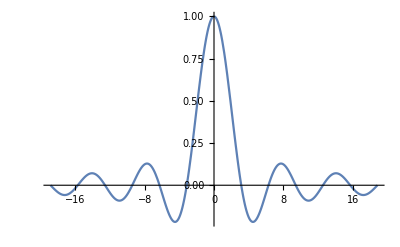

```mathematica
f[x_]:=Sin[x]/x;
Plot[f[x],{x,-6 Pi,6 Pi},PlotRange->All]
```

```mathematica
Limit[f[x],x->Infinity]
```

0

```mathematica
Limit[f[x],x->∞]
```

0

```mathematica
Limit[Sin[3 x]/Tan[7 x],x->0]
```

3/7

```mathematica
Limit[(2 x^3-3 x+1)/(-5 x^2+π),x->∞]
```

-∞

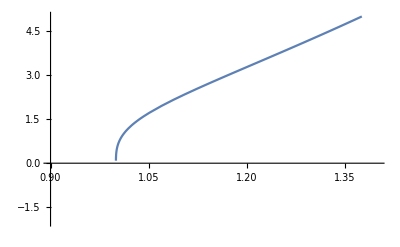

```mathematica
g[x_]:=(x^3-1)^(4/3) (x-1)^-1
Plot[g[x],{x,0.5,1.4},PlotRange->{-2,5},AxesOrigin->{0.9,0}]
```

```mathematica
Limit[g[x],x->1]
```

0

```mathematica
Clear[g1]
```

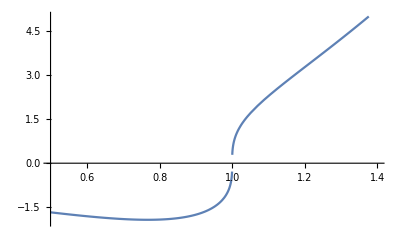

```mathematica
g1[x_]:=((x^3-1)^4)^(1/3) (x-1)^-1
Plot[g1[x],{x,0.5,1.4},PlotRange->{-2,5}]
```

```mathematica
Limit[g1[x],x->1]
```

0

```mathematica
Limit[(x-Cos[2 x])/(x^2+1),x->0]
```

-1

```mathematica
Limit[x/Log[x],x->∞]
```

∞

```mathematica
Limit[(x^4-2 x+1)/(3 x^4+x^3-2),x->∞]
```

1/3

```mathematica
Limit[(x Sin[2 x])/(Cos[x+π/2] Tan[3 x]),x->0]
```

-2/3

```mathematica
f[x_]:=If[x<1,2 x+3,6 Cos[Pi x]]
Limit[f[x],x->1,Direction->2]
Limit[f[x],x->1,Direction->-1]
```

5

-6

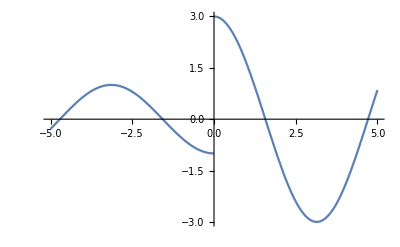

```mathematica
f1[x_]:=(Cos[x] (2 x+Abs[x]))/Abs[x]
Plot[f1[x],{x,-5,5}]
```

```mathematica
Limit[f1[x],x->0,Direction->1]
```

-1

```mathematica
Limit[f1[x],x->0,Direction->-1]
```

3

```mathematica
Limit[f1[x],x->0]
```

Indeterminate

```mathematica
Clear[f,g]
```

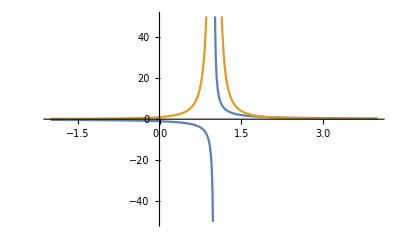

```mathematica
f[x_]:=1/(x-1);
g[x_]:=1/(x-1)^2;
Plot[{f[x],g[x]},{x,-2,4},PlotRange->{-50,50}]
```

```mathematica
{Limit[f[x],x->1,Direction->1],Limit[f[x],x->1,Direction->-1]}
```

{π/4,π/4}

```mathematica
{Limit[g[x],x->1,Direction->1],Limit[g[x],x->1,Direction->-1]}
```

{∞,∞}

```mathematica
f[x_]:=ArcTan[x]
Limit[f[x],x->1]
```

π/4

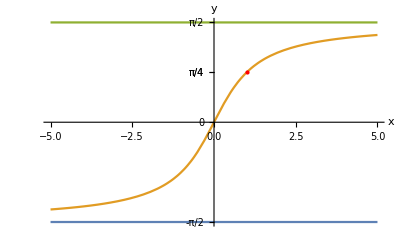

```mathematica
g1=Plot[{-π/2,f[x],π/2},{x,-5,5}];
g2=Graphics[{PointSize[Medium],Red,Point[{1,Limit[f[x],x->1]}]}];
Show[g1,g2,Ticks->{Automatic,{-π/2,π/4,0,π/4,π/2}},AxesLabel->{x,y}]
```

```mathematica
{Limit[f[x],x->∞],Limit[f[x],x->∞]}
```

{π/2,π/2}

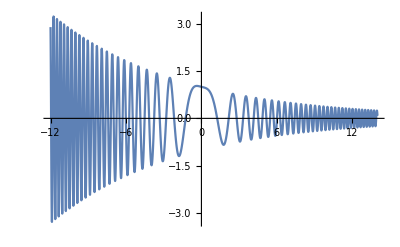

```mathematica
f[x_]:=ⅇ^(-x/10) Cos[x^2]; (* Cos[2x] *)
Plot[f[x],{x,-12,14},PlotRange->All]
```

```mathematica
{Limit[f[x],x->-∞],Limit[f[x],x->∞]}
```

{0,0}

```mathematica
f[x_]:=(2 Sin[x]+Cos[x]-1)/(3 x);
Limit[f[x],x->0]
```

2/3

```mathematica
Limit[(3 (Sin[x])^2+Cos[x]-1)/(5 x^2),x->0]
```

1/2

```mathematica
D[3 (Sin[x])^2+Cos[x]-1,x]
D[3 (Sin[x])^2+Cos[x]-1,{x,2}]
D[3 (Sin[x])^2+Cos[x]-1,{x,2}]/.x->0
```

-Sin[x]+6 Cos[x] Sin[x]

-Cos[x]+3 (2 Cos[x]^2-2 Sin[x]^2)

5

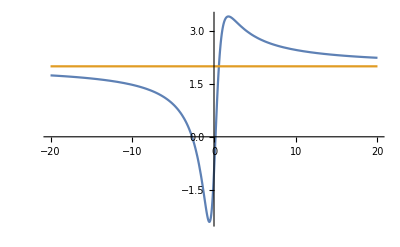

{2,2}

```mathematica
f[x_]:=(2 x^2+5 x-1)/(x^2+1);
Plot[{f[x],2},{x,-20,20},PlotRange->All]
{Limit[f[x],x->-∞],Limit[f[x],x->∞]}
```

{Indeterminate,2}

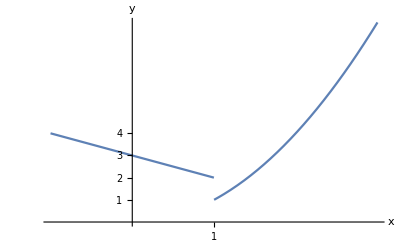

```mathematica
f[x_]:=If[x<1,3-x,x^2]
{Limit[f[x],x->1,Direction->0],Limit[f[x],x->1,Direction->3]}
Plot[f[x],{x,-1,3},Ticks->{{1},{1,2,3,4}},AxesLabel->{x,y},AxesOrigin->{0,0},Exclusions->{1}]
```

```mathematica
Limit[(ⅇ^x-ⅇ^Tan[x])/(x-Tan[x]),x->0]
```

1

```mathematica
Limit[(Log[x]-Log[2])/(x^2-5 x+6),x->2]
```

-1/2

```mathematica
Limit[1/x^3 (a^(√(1+x))-a^(1+x/2+x^2/8)),x->0,Assumptions->a>0]
```

Indeterminate

```mathematica
(* Пресмятане на крайни суми, суми на редове и пройзведения *)
Sum[1/3^k,{k,0,10}]
∑_(k=0)^10 1/3^k
```

88573/59049

88573/59049

```mathematica
Sum[1/3^k,{k,0,n}]
```

1/2 3^-n (-1+3^(1+n))

```mathematica
Simplify[%]
```

3/2-3^-n/2

```mathematica
∑_(k=5)^∞ 1/2^k
```

1/16

```mathematica
Limit[∑_(k=1)^n (7 k-1)/3^k,n->∞]
```

19/4

```mathematica
Sum[(7 k^2-Log[k])/(k! 2^k),{k,1,∞}]
∑_(k=1)^∞ (7 k^2-Log[k])/(k!2^k)
```

∑_(k=1)^∞ (2^-k (7 k^2-Log[k]))/(k!)

∑_(k=1)^∞ (2^-k (7 k^2-Log[k]))/(k!)

```mathematica
∑_(k=1)^n 1/(k (k+1))
```

1-1/(1+n)

```mathematica
NSum[(7 k^2-Log[k])/(k! 2^k),{k,1,∞},WorkingPrecision->20]
N[∑_(k=1)^∞ (7 k^2-Log[k])/(k!2^k),20]
```

8.5421841376119664697

8.5421841376119664697

```mathematica
∑_(k=1)^n 1/(k (k+1))
```

1-1/(1+n)

```mathematica
Simplify[%]
```

n/(1+n)

```mathematica
∑_(k=1)^n k^2
```

1/6 n (1+n) (1+2 n)

```mathematica
p=12;
∑_(k=1)^n k^p
```

1/2730 n (1+n) (1+2 n) (-691+2073 n-287 n^2-3285 n^3+1420 n^4+2310 n^5-1190 n^6-1050 n^7+525 n^8+525 n^9+105 n^10)

```mathematica
∑_(k=1)^∞ ∑_(j=1)^k 1/(j^2 (k+1)^2)
```

π^4/120

```mathematica
∑_(k=0)^∞ 3^k/(k!)
```

ⅇ^3

```mathematica
NSum[3^k/(k!),{k,0,Infinity}]
```

20.0855

```mathematica
Product[(2 k-1)^2,{k,1,5}]
∏_(k=1)^5 (2 k-1)^2
```

893025

893025

```mathematica
∏_(k=1)^n k^3
```

(n!)^3

```mathematica
∏_(k=2)^∞ (1-1/k^4)
```

Sinh[π]/(4 π)

```mathematica
NProduct[1-1/k^2,{k,2,∞}]
```

0.5

```mathematica
(* Производни *)
f[x_]:=1/3 x^3-2 x+5;
f'[x]
f''[x]
f'''[x]
```

-2+x^2

2 x

2

```mathematica
f[x_]:=2 x^(4/3)-Log[x]+x Cos[x];
f'[x]
f''[x]
f'''''[x]
```

-1/x+(8 x^(1/3))/3+Cos[x]-x Sin[x]

1/x^2+8/(9 x^(2/3))-x Cos[x]-2 Sin[x]

-24/x^5-640/(243 x^(11/3))+5 Cos[x]-x Sin[x]

```mathematica
f'[x]/.x->1
f''[x]/.x->π
```

5/3+Cos[1]-Sin[1]

1/π^2+8/(9 π^(2/3))+π

```mathematica
D[f[x],x]
D[f[x],{x,2}]
D[f[x],{x,5}]
```

-1/x+(8 x^(1/3))/3+Cos[x]-x Sin[x]

1/x^2+8/(9 x^(2/3))-x Cos[x]-2 Sin[x]

-24/x^5-640/(243 x^(11/3))+5 Cos[x]-x Sin[x]

```mathematica
f'[1]
f''[-π]
```

5/3+Cos[1]-Sin[1]

1/π^2-(8 (-1)^(1/3))/(9 π^(2/3))-π

```mathematica
D[f[x],x]/.x->1
```

5/3+Cos[1]-Sin[1]

```mathematica
D[f[x],{x,9}]/.x->1//N
f'''''''''[x]
```

-42018.5

-40320/x^9-33510400/(19683 x^(23/3))+9 Cos[x]-x Sin[x]

```mathematica
f[x_]:=If[x<0,-2 x,x^2+3 x]
f'[x]
f''[x]
```

If[x<0,-2,3+2 x]

If[x<0,0,2]

```mathematica
g[x_,y_,z_]:=2 x^(4/3) y^2 z-Log[x] Sin[z]+3 x Cos[y];
D[g[x,y,z],x]
D[g[x,y,z],{y,2}]
D[g[x,y,z],x,{y,2},z]
```

8/3 x^(1/3) y^2 z+3 Cos[y]-Sin[z]/x

4 x^(4/3) z-3 x Cos[y]

(16 x^(1/3))/3

```mathematica
D[g[x,y,z],x]/.x->1
D[g[x,y,z],x]/.{x->1,y->0,z->0}
D[g[x,y,z],x,{y,2},z]/.{x->8,y->-2,z->Pi}
```

(8 y^2 z)/3+3 Cos[y]-Sin[z]

3

32/3

```mathematica
h[x_,y_,z_]:=2 x^(4/3) y^2 z-Log[x] Sin[z]+3 x Cos[y];
D[h[x,y,z], x]
D[h[x,y,z], y,z]
D[h[x,y,z], x,y,y,z,z]
```

8/3 x^(1/3) y^2 z+3 Cos[y]-Sin[z]/x

4 x^(4/3) y

0

```mathematica
(* Ред на Тейлор *)
Series[ⅇ^x,{x,0,10}]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+O[x]^11

```mathematica
Normal[%]
```

1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800

```mathematica
f[x_]:=Log[x+1];
Series[f[x],{x,0,8}]
Normal[Series[f[x],{x,0,8}]]
```

x-x^2/2+x^3/3-x^4/4+x^5/5-x^6/6+x^7/7-x^8/8+O[x]^9

x-x^2/2+x^3/3-x^4/4+x^5/5-x^6/6+x^7/7-x^8/8

```mathematica
f[x_]:=(ⅇ^(ArcTan[x]-x+1)+Cos[x])/(x^2+1)
n=5;
Series[f[x],{x,0,n}]
Normal[Series[f[x],{x,0,n}]]
```

(1+ⅇ)+(-3/2-ⅇ) x^2-(ⅇ x^3)/3+(37/24+ⅇ) x^4+(8 ⅇ x^5)/15+O[x]^6

1+ⅇ+(-3/2-ⅇ) x^2-(ⅇ x^3)/3+(37/24+ⅇ) x^4+(8 ⅇ x^5)/15

```mathematica
f[x_,y_]:=ⅇ^(2 x+3 y) Sin[x];
n=3;
Series[f[x,y],{x,0,n},{y,0,n}]//Normal
```

x (1+3 y+(9 y^2)/2+(9 y^3)/2)+x^3 (11/6+(11 y)/2+(33 y^2)/4+(33 y^3)/4)+x^2 (2+6 y+9 y^2+9 y^3)

-1+4 Sin[x]-2 Sin[2 x]+4/3 Sin[3 x]-Sin[4 x]+4/5 Sin[5 x]-2/3 Sin[6 x]+4/7 Sin[7 x]-1/2 Sin[8 x]+4/9 Sin[9 x]-2/5 Sin[10 x]

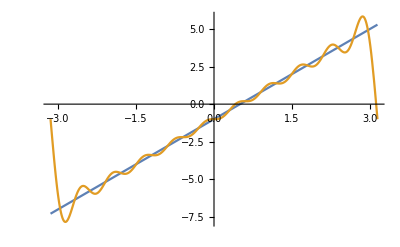

```mathematica
(* Ред на Фурие *)
f[x_]:=2 x-1;
FourierSeries[f[x],x,10]//ExpToTrig
Plot[{f[x],%},{x,-π,π}]
```

π/2-(4 Cos[x])/π-(4 Cos[3 x])/(9 π)

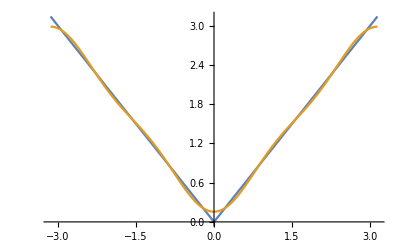

```mathematica
f[x_]:=Abs[x];
FourierSeries[f[x],x,3]//ExpToTrig
Plot[{f[x],%},{x,-π,π}]
```

(2 ⅈ ⅇ^(-ⅈ x))/π-(2 ⅈ ⅇ^(ⅈ x))/π+(2 ⅈ ⅇ^(-3 ⅈ x))/(3 π)-(2 ⅈ ⅇ^(3 ⅈ x))/(3 π)+(2 ⅈ ⅇ^(-5 ⅈ x))/(5 π)-(2 ⅈ ⅇ^(5 ⅈ x))/(5 π)+(2 ⅈ ⅇ^(-7 ⅈ x))/(7 π)-(2 ⅈ ⅇ^(7 ⅈ x))/(7 π)+(2 ⅈ ⅇ^(-9 ⅈ x))/(9 π)-(2 ⅈ ⅇ^(9 ⅈ x))/(9 π)

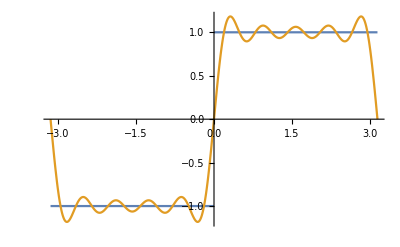

```mathematica
f[x_]:=Which[x<0,-1,x≥0,1];
FourierSeries[f[x],x,10]
Plot[{f[x],%},{x,-π,π}]
```

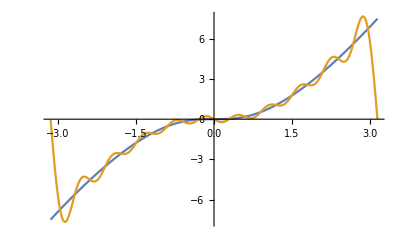

```mathematica
f[x_]:=x Log[x^2+1]
FourierSeries[f[x],x,10];
Plot[{f[x],%},{x,-π,π}]
```

```mathematica
g[x_,y_]:=x^2 y
FourierCosSeries[g[x,y],{x,y},{3,3}]//ExpToTrig
Plot3D[{g[x,y],%},{x,-π,π},{y,-π,π}]
```

(2 π^3)/3-4 π Cos[x]+π Cos[2 x]-4/9 π Cos[3 x]-8/3 π Cos[y]+(16 Cos[x] Cos[y])/π-(4 Cos[2 x] Cos[y])/π+(16 Cos[3 x] Cos[y])/(9 π)-8/27 π Cos[3 y]+(16 Cos[x] Cos[3 y])/(9 π)-(4 Cos[2 x] Cos[3 y])/(9 π)+(16 Cos[3 x] Cos[3 y])/(81 π)

-Graphics3D-